```mathematica
ν=((299792458)/({34.4,37.1,40,43.7,48.1}*10^(-12)))/(10^(18)) (*EHz = 10^18 Hz*)
```

{8.7149,8.08066,149896229/20000000,6.86024,6.23269}

```mathematica
V={35,32.5,30,27.5,25}; (*kV*)
```

```mathematica
data=Transpose[{ν,V}]
```

{{8.7149,35},{8.08066,32.5},{149896229/20000000,30},{6.86024,27.5},{6.23269,25}}

```mathematica
fit=NonlinearModelFit[data,A*x+B,{A,B},x]
```

FittedModel[…]

```mathematica
fit[{"BestFit","ParameterTable"}]
```

{-0.217068+4.04152 x, | Estimate | Standard Error | t-Statistic | P-Value
A | 4.04152 | 0.0290809 | 138.975 | 8.21445×10^-7
B | -0.217068 | 0.218911 | -0.991582 | 0.394498}

```mathematica
plotfit=Plot[fit[x],{x,0,100},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{6.0,8.8},{24.3,35.8}},Frame->True,FrameLabel->{Style["ν / EHz",Bold,16],Style["V / kV",16,Bold]}];
```

```mathematica
plotdata=ListPlot[data,PlotStyle->{Black,Thickness[0.003]}];
```

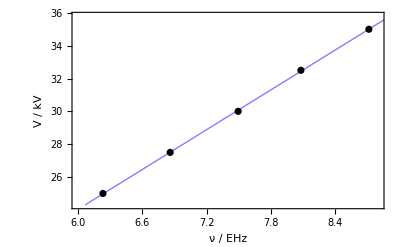

```mathematica
Show[plotfit,plotdata]
```

```mathematica
Aaj=4.041519791400553;
```

```mathematica
errAj=0.029080879127361545;
```

```mathematica
h=Aaj*(1.602*10^(-19))*(10^3)/(10^18) (*J s*)
```

6.47451×10^-34

```mathematica
errh=errAj*(1.602*10^(-19))*(10^3)/(10^18) (*J s*)
```

4.65876×10^-36